```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Solving for the pion γ and β in terms of kinetic energy of pion Eπ (arbitrary parameter but of order ~ 500 MeV)

```mathematica
Solve[(γ-1)mπ==Eπ/.γ->1/Sqrt[1-β^2],β]//Simplify
```

{{β→-(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)},{β→(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)}}

```mathematica
(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)/.{mπ->140}//Expand
```

(√Eπ √(280+Eπ))/(140+Eπ)

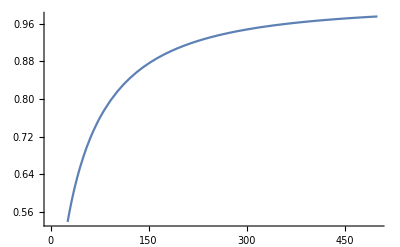

```mathematica
Plot[(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)/.{mπ->140},{Eπ,0,500}]
```

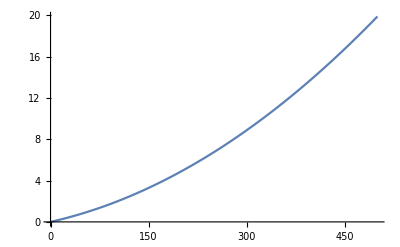

```mathematica
Plot[Emax/.{mπ->140,me->0.5},{Eπ,0,500}]
```

#### Define Emax (in the simplest approximation)

```mathematica
Emax:=((2me*β^2 γ^2)/.{γ->1/Sqrt[1-β^2]})/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)
```

```mathematica
Emax//FullSimplify
```

(2 Eπ me (Eπ+2 mπ))/mπ^2

```mathematica
Emax2:=( 2me*Z^2*γ^2*α^2/.{γ->1/Sqrt[1-β^2]})/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)
```

```mathematica
Emax2/.{Z->1}//FullSimplify
```

(2 me (Eπ+mπ)^2 α^2)/mπ^2

```mathematica
dσdE=2Pi*(α^2 Z^2)/(me*β^2*Ed^2)(1-β^2 Ed/emax)//FullSimplify;
```

```mathematica
dEdx=Integrate[dσdE*n*Ed,Ed]//FullSimplify
```

(2 n π Z^2 α^2 (-(Ed β^2)/emax+Log[Ed]))/(me β^2)

```mathematica
(dEdx/.Ed->emax)-(dEdx/.Ed->emin)
```

(2 n π Z^2 α^2 (-β^2+Log[emax]))/(me β^2)-(2 n π Z^2 α^2 (-(emin β^2)/emax+Log[emin]))/(me β^2)

```mathematica
stoppingpower=2Pi*(n*Z^2*α^2)/(me*β^2)(Log[Emax/emin]-β^2)/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)//FullSimplify;
```

```mathematica
stoppingpower/.{n->8,me->0.511,emin->10^-10,α->1/137,mπ->139.57,Z->1}
```

(0.00524092 (-Eπ (279.14+Eπ)+(139.57+Eπ)^2 Log[524646. Eπ (279.14+Eπ)]))/(Eπ (279.14+Eπ))

#### Express number density in units of MeV

```mathematica
Convert[10^33/Centimeter^3*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]//N
```

8. ElectronVolt^3 Mega^3

#### Plot of stopping power, with numerics

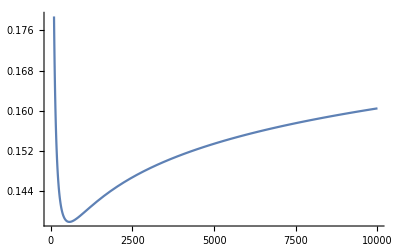

```mathematica
Plot[stoppingpower/.{n->8,me->0.511,emin->10^-10,α->1/137,mπ->139.57,Z->1},{Eπ,0,10000}]
```

#### Comparing with the PDG, which measures dE/dx in MeV g^-1 cm^2 for differing materials (normalized by density) and finds O(1) values:

```mathematica
Convert[0.15(Mega ElectronVolt)^2*( (5*10^9 Gram)/Centimeter^3)^-1*1/(200 Mega ElectronVolt*Fermi),(Mega ElectronVolt*Centimeter^2/Gram)]
```

(1.5 Centimeter^2 ElectronVolt Mega)/Gram

#### Range for a typical value of Eπ

```mathematica
NIntegrate[stoppingpower^-1/.{n->8,me->0.511,emin->10^-10,α->1/137,mπ->139.57,Z->1},{Eπ,0,500}]
```

3096.49

#### Plot R for varying values of Eπ

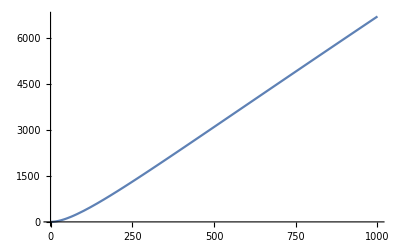

```mathematica
Plot[NIntegrate[stoppingpower^-1/.{n->8,me->0.511,emin->10^-10,α->1/137,mπ->139.57,Z->1},{Eπ,0,d}],{d,0,1000}]
```

```mathematica
2*0.5*25*(1/137)^2//N
```

0.00133198

#### In terms of PDG units, which gives range (normalized by density) of order O(1000 gm cm^-2):

```mathematica
Convert[3000/(Mega ElectronVolt)*( (5*10^9 Gram)/Centimeter^3)*(200 Mega ElectronVolt*Fermi),Gram/Centimeter^2]
```

(300 Gram)/Centimeter^2

#### Range (cm)

```mathematica
Convert[3000/(Mega ElectronVolt)(200 Mega ElectronVolt*Fermi),Centimeter]//N
```

6.×10^-8 Centimeter

#### As a check, electromagnetic scattering off nuclei does not affect range significantly.

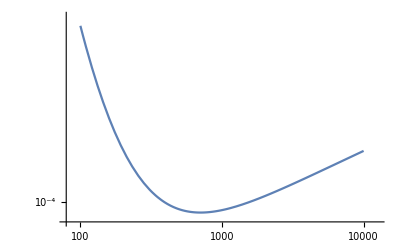

```mathematica
LogLogPlot[stoppingpower/.{n->8,me->1000*12,emin->10^-10,α->1/137,mπ->139.57,Z->Sqrt[12]},{Eπ,100,10000}]
```

#### Now incorporate Pauli-Blocking.

#### For relativistic fermi gas:

```mathematica
npaulirel:=Integrate[e^2/Pi^2,{e,Ef-Ed,Ef}]
```

```mathematica
npaulirel/.{Ed->Ef}
```

Ef^3/(3 π^2)

```mathematica
(3 Pi^2 n)^(1/3)/.n->8//N
```

6.18734

```mathematica
plotrel=Plot[npaulirel/.{Ef->2 3^(1/3) π^(2/3),n->8},{Ed,0,2 3^(1/3) π^(2/3)}];
```

#### For nonrelativistic fermi gas:

```mathematica
npaulinonrel:=Integrate[1/(2 Pi^2)*(2me)^(3/2)e^(1/2),{e,Ef-Ed,Ef}]
```

```mathematica
1/(2me)*(3 Pi^2 n)^(2/3)/.{n->8,me->0.511}
```

37.459

#### Using naive pauliblocking factor (Ed/Ef), where Ed is deposited energy

```mathematica
naiveplotrel=Plot[n*(Ed/Ef)/.{Ef->2 3^(1/3) π^(2/3),n->8},{Ed,0,2 3^(1/3) π^(2/3)}];
```

#### Comparing “effective” number density available for depositing energy Ed, with upper end of plot being Fermi energy.

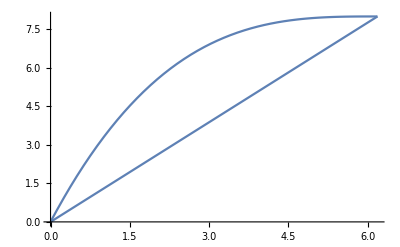

```mathematica
Show[plotrel,naiveplotrel]
```

```mathematica
dσdE
```

(2 π Z^2 α^2 (1-(Ed β^2)/emax))/(Ed^2 me β^2)

```mathematica
npaulirel
```

Ed^3/(3 π^2)-(Ed^2 Ef)/π^2+(Ed Ef^2)/π^2

```mathematica
dedxrel:=Integrate[dσdE*npaulirel*Ed,{Ed,0,Min[Ef,emax]}]//Expand
```

```mathematica
dedxnonrel:=Integrate[dσdE*npaulinonrel*Ed,{Ed,0,Min[Ef,emax]}]//Expand
```

```mathematica
dedxnaive:=Integrate[dσdE*n(Ed/Ef)*Ed,{Ed,0,Min[Ef,emax]}]//Expand
```

```mathematica
dedxrel
```

(2 Ef^2 Z^2 α^2 Min[Ef,emax])/(me π β^2)-(Ef^2 Z^2 α^2 Min[Ef,emax]^2)/(emax me π)-(Ef Z^2 α^2 Min[Ef,emax]^2)/(me π β^2)+(2 Ef Z^2 α^2 Min[Ef,emax]^3)/(3 emax me π)+(2 Z^2 α^2 Min[Ef,emax]^3)/(9 me π β^2)-(Z^2 α^2 Min[Ef,emax]^4)/(6 emax me π)

```mathematica
dedxnaive
```

(2 n π Z^2 α^2 Min[Ef,emax])/(Ef me β^2)-(n π Z^2 α^2 Min[Ef,emax]^2)/(Ef emax me)

```mathematica
dedxnorm:=(Integrate[dσdE*n*Ed,Ed]/.Ed->Max[Ef,emax])-(Integrate[dσdE*n*Ed,Ed]/.Ed->Ef)//Expand
```

```mathematica
dedxnorm
```

(2 Ef n π Z^2 α^2)/(emax me)-(2 n π Z^2 α^2 Log[Ef])/(me β^2)+(2 n π Z^2 α^2 Log[Max[Ef,emax]])/(me β^2)-(2 n π Z^2 α^2 Max[Ef,emax])/(emax me)

```mathematica
dedxpauli:=((dedxrel+dedxnorm/.{emax->Emax,Ef->(3 Pi^2 n)^(1/3)})/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ))/.{me->0.511,α->1/137,mπ->139.57,Z->1}
```

```mathematica
dedxpauli/.n->0.008//Simplify
```

Piecewise[{{(0.140813+0.00268208 Eπ+9.60836×10^-6 Eπ^2)/(279.14 Eπ+Eπ^2), Eπ==-316.412||Eπ==37.2721}, {1/(279.14 Eπ+Eπ^2)(1.38778×10^-17+0.00724934 Eπ-7.88255×10^-6 Eπ^2-2.0109×10^-7 Eπ^3+1.62774×10^-9 Eπ^4+2.47618×10^-11 Eπ^5+1.2639×10^-13 Eπ^6+2.97302×10^-16 Eπ^7+2.66266×10^-19 Eπ^8), -316.412<Eπ<37.2721}, {(0.251633+0.00192146 Eπ+6.8835×10^-6 Eπ^2+(0.102092+0.00146295 Eπ+5.24092×10^-6 Eπ^2) Log[0.0000524646 Eπ (279.14+Eπ)])/(Eπ (279.14+Eπ)), True}}]

```mathematica
Plot[dedxpauli/.n->0.008,{Eπ,0,1000}]
```

$Aborted

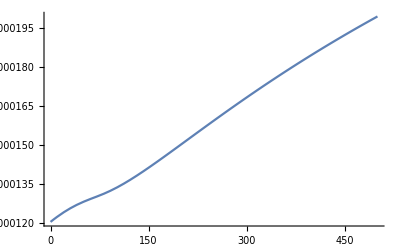

```mathematica
Plot[dedxpauli/.n->0.08,{Eπ,0,500}]
```

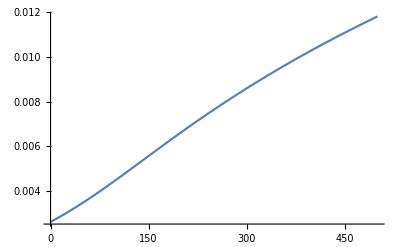

```mathematica
Plot[dedxpauli/.n->8,{Eπ,0,500}]
```

```mathematica
Table[Convert[NIntegrate[dedxpauli^-1,{Eπ,0,500}]/(Mega ElectronVolt)(200 Mega ElectronVolt*Fermi),Centimeter],{n,{0.008,0.08,0.8,8}}]//N
```

{0.000473582 Centimeter,0.0000640821 Centimeter,9.57599×10^-6 Centimeter,1.60798×10^-6 Centimeter}

```mathematica
2*0.511*1^2*(1/137)^2
```

0.0000544515